```mathematica
Quit[]
```

```mathematica
SetDirectory["/Users/saraditsch/Desctop/Wtt/Mathematica"];
```

SetDirectory::cdir: Cannot set current directory to /Users/saraditsch/Desctop/Wtt/Mathematica.

```mathematica
SetDirectory["/scratch/ge84fet/Wtt/Mathematica/MMatrix"];
```

```mathematica
$LoadAddOns = {"FeynArts"};
Quiet[Check[Get["FeynCalc`"],Print["FeynCalc is not available."]]]
$FAVerbose=0;
FCCheckVersion[9,3,0];
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
MakeBoxes[p1,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(1\)]\)";
MakeBoxes[p2,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(2\)]\)";
MakeBoxes[p3,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(3\)]\)";
MakeBoxes[p4,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(4\)]\)";
MakeBoxes[p5,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(5\)]\)";
```

```mathematica
SetMandelstam[s,{p1,p2,p3,p4,p5},{0,0,SMP["m_t"],SMP["m_t"],SMP["m_W"]}];
Identities={s[1,5] -> 2SMP["m_t"]^2+SMP["m_W"]^2-s[1,2]-s[1,3]-s[1,4], s[2,5]-> 2SMP["m_t"]^2+SMP["m_W"]^2-s[1,2]-s[2,3]-s[2,4], s[3,5]-> 3SMP["m_t"]^2+SMP["m_W"]^2-s[1,3]-s[2,3]-s[3,4], s[4,5]-> 3SMP["m_t"]^2+SMP["m_W"]^2-s[1,4]-s[2,4]-s[3,4]}/.s[3,4]->-(s[2,4]+s[2,3]+s[1,4]+s[1,3]+s[1,2]-4*SMP["m_t"]^2-SMP["m_W"]^2);
AppendTo[Identities,s[3,4]->-(s[2,4]+s[2,3]+s[1,4]+s[1,3]+s[1,2]-4*SMP["m_t"]^2-SMP["m_W"]^2)];
Massless={SMP["m_d"]->0,SMP["m_u"]->0};
```

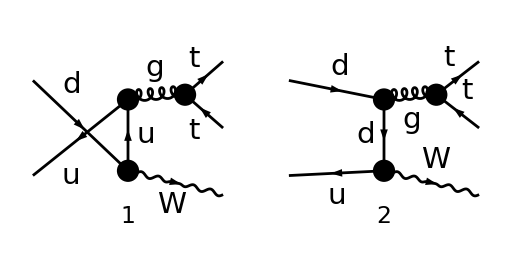

```mathematica
diags=InsertFields[CreateTopologies[0,2->3],{F[4,{1}],-F[3,{1}]}->{F[3,{3}],-F[3,{3}],V[3]},InsertionLevel->{Classes},Model-> "SMQCD",ExcludeParticles->{S[_],V[3],V[1],V[2]}];
Paint[diags,ColumnsXRows->{2,1},Numbering->Simple,SheetHeader->None,ImageSize->{512,256}];
```

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4,p5},ChangeDimension->4,List->False,SMP->True,Contract->True,DropSumOver->True,UndoChiralSplittings->True]//.Massless
```

(e g_s^2 T_Col2Col1^Glu6 T_Col3Col4^Glu6 (φ(OverBar[p_3],m_t)).(γ̄)^Lor2.(φ(-OverBar[p_4],m_t)) (φ(-OverBar[p_2])).(γ̄)^Lor2.(γ̄·(-OverBar[p_2]+OverBar[p_3]+OverBar[p_4])).(γ̄·(ε̄)^*(p_5)).(γ̄)^7.(φ(OverBar[p_1])))/(√2 (sin(θ_W)) (OverBar[p_3]+OverBar[p_4])^2 (OverBar[p_2]-OverBar[p_3]-OverBar[p_4])^2)+(e g_s^2 T_Col2Col1^Glu6 T_Col3Col4^Glu6 (φ(OverBar[p_3],m_t)).(γ̄)^Lor2.(φ(-OverBar[p_4],m_t)) (φ(-OverBar[p_2])).(γ̄·(ε̄)^*(p_5)).(γ̄)^7.(γ̄·(OverBar[p_5]-OverBar[p_2])).(γ̄)^Lor2.(φ(OverBar[p_1])))/(√2 (sin(θ_W)) (OverBar[p_2]-OverBar[p_5])^2 (OverBar[p_3]+OverBar[p_4])^2)

```mathematica
ampSquared[0] = (1/2*1/3)^4*Simplify[(DoPolarizationSums[DiracSimplify[FermionSpinSum[(SUNSimplify[FeynAmpDenominatorExplicit[(1/SUNN^2)*(amp[0]*ComplexConjugate[amp[0]])], Explicit -> True, SUNNToCACF -> False])]], p5] //. Identities)//.Massless]
```

((N^2-1) e^2 g_s^4 (1280 m_W^2 m_t^10+256 s(1,2) m_t^10+416 m_W^4 m_t^8-288 (s(1,2))^2 m_t^8-2368 s(1,2) m_W^2 m_t^8-1184 s(1,3) m_W^2 m_t^8-1184 s(1,4) m_W^2 m_t^8-1696 s(2,3) m_W^2 m_t^8-1696 s(2,4) m_W^2 m_t^8-32 s(1,2) s(1,3) m_t^8-32 s(1,2) s(1,4) m_t^8-544 s(1,2) s(2,3) m_t^8-544 s(1,2) s(2,4) m_t^8+96 m_W^6 m_t^6-928 s(1,2) m_W^4 m_t^6-352 s(1,3) m_W^4 m_t^6-352 s(1,4) m_W^4 m_t^6-416 s(2,3) m_W^4 m_t^6-416 s(2,4) m_W^4 m_t^6+96 (s(1,2))^3 m_t^6+480 s(1,2) (s(2,3))^2 m_t^6+480 s(1,2) (s(2,4))^2 m_t^6+1760 (s(1,2))^2 m_W^2 m_t^6+400 (s(1,3))^2 m_W^2 m_t^6+400 (s(1,4))^2 m_W^2 m_t^6+864 (s(2,3))^2 m_W^2 m_t^6+864 (s(2,4))^2 m_W^2 m_t^6+1728 s(1,2) s(1,3) m_W^2 m_t^6+1728 s(1,2) s(1,4) m_W^2 m_t^6+608 s(1,3) s(1,4) m_W^2 m_t^6+2496 s(1,2) s(2,3) m_W^2 m_t^6+1456 s(1,3) s(2,3) m_W^2 m_t^6+1360 s(1,4) s(2,3) m_W^2 m_t^6+2496 s(1,2) s(2,4) m_W^2 m_t^6+1360 s(1,3) s(2,4) m_W^2 m_t^6+1456 s(1,4) s(2,4) m_W^2 m_t^6+1472 s(2,3) s(2,4) m_W^2 m_t^6+32 (s(1,2))^2 s(1,3) m_t^6+32 (s(1,2))^2 s(1,4) m_t^6+480 (s(1,2))^2 s(2,3) m_t^6+8 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(2,3) m_t^6-8 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(2,3) m_t^6+64 s(1,2) s(1,3) s(2,3) m_t^6+64 s(1,2) s(1,4) s(2,3) m_t^6+480 (s(1,2))^2 s(2,4) m_t^6-8 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(2,4) m_t^6+8 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(2,4) m_t^6+64 s(1,2) s(1,3) s(2,4) m_t^6+64 s(1,2) s(1,4) s(2,4) m_t^6+832 s(1,2) s(2,3) s(2,4) m_t^6+8 m_W^8 m_t^4-64 s(1,3) m_W^6 m_t^4-64 s(1,4) m_W^6 m_t^4-64 s(2,3) m_W^6 m_t^4-64 s(2,4) m_W^6 m_t^4-8 (s(1,2))^4 m_t^4+480 (s(1,2))^2 m_W^4 m_t^4+116 (s(1,3))^2 m_W^4 m_t^4+116 (s(1,4))^2 m_W^4 m_t^4+116 (s(2,3))^2 m_W^4 m_t^4+116 (s(2,4))^2 m_W^4 m_t^4+408 s(1,2) s(1,3) m_W^4 m_t^4+408 s(1,2) s(1,4) m_W^4 m_t^4+104 s(1,3) s(1,4) m_W^4 m_t^4+808 s(1,2) s(2,3) m_W^4 m_t^4+368 s(1,3) s(2,3) m_W^4 m_t^4+256 s(1,4) s(2,3) m_W^4 m_t^4+808 s(1,2) s(2,4) m_W^4 m_t^4+256 s(1,3) s(2,4) m_W^4 m_t^4+368 s(1,4) s(2,4) m_W^4 m_t^4+296 s(2,3) s(2,4) m_W^4 m_t^4-216 s(1,2) (s(2,3))^3 m_t^4-216 s(1,2) (s(2,4))^3 m_t^4-328 (s(1,2))^2 (s(2,3))^2 m_t^4-12 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(2,3))^2 m_t^4+8 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(2,3))^2 m_t^4-56 s(1,2) s(1,3) (s(2,3))^2 m_t^4-56 s(1,2) s(1,4) (s(2,3))^2 m_t^4-328 (s(1,2))^2 (s(2,4))^2 m_t^4+12 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(2,4))^2 m_t^4-8 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(2,4))^2 m_t^4-56 s(1,2) s(1,3) (s(2,4))^2 m_t^4-56 s(1,2) s(1,4) (s(2,4))^2 m_t^4-488 s(1,2) s(2,3) (s(2,4))^2 m_t^4-656 (s(1,2))^3 m_W^2 m_t^4-64 (s(1,3))^3 m_W^2 m_t^4-64 (s(1,4))^3 m_W^2 m_t^4-208 (s(2,3))^3 m_W^2 m_t^4-208 (s(2,4))^3 m_W^2 m_t^4-432 s(1,2) (s(1,3))^2 m_W^2 m_t^4-432 s(1,2) (s(1,4))^2 m_W^2 m_t^4-112 s(1,3) (s(1,4))^2 m_W^2 m_t^4-952 s(1,2) (s(2,3))^2 m_W^2 m_t^4-664 s(1,3) (s(2,3))^2 m_W^2 m_t^4-584 s(1,4) (s(2,3))^2 m_W^2 m_t^4-952 s(1,2) (s(2,4))^2 m_W^2 m_t^4-584 s(1,3) (s(2,4))^2 m_W^2 m_t^4-664 s(1,4) (s(2,4))^2 m_W^2 m_t^4-416 s(2,3) (s(2,4))^2 m_W^2 m_t^4-944 (s(1,2))^2 s(1,3) m_W^2 m_t^4-944 (s(1,2))^2 s(1,4) m_W^2 m_t^4-112 (s(1,3))^2 s(1,4) m_W^2 m_t^4-688 s(1,2) s(1,3) s(1,4) m_W^2 m_t^4-1392 (s(1,2))^2 s(2,3) m_W^2 m_t^4-424 (s(1,3))^2 s(2,3) m_W^2 m_t^4-360 (s(1,4))^2 s(2,3) m_W^2 m_t^4-8 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_2]OverBar[p_3]OverBar[p_4]) s(2,3) m_W^2 m_t^4-8 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(2,3) m_W^2 m_t^4+8 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(2,3) m_W^2 m_t^4-1544 s(1,2) s(1,3) s(2,3) m_W^2 m_t^4-1480 s(1,2) s(1,4) s(2,3) m_W^2 m_t^4-576 s(1,3) s(1,4) s(2,3) m_W^2 m_t^4-1392 (s(1,2))^2 s(2,4) m_W^2 m_t^4-360 (s(1,3))^2 s(2,4) m_W^2 m_t^4-424 (s(1,4))^2 s(2,4) m_W^2 m_t^4-416 (s(2,3))^2 s(2,4) m_W^2 m_t^4+8 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_2]OverBar[p_3]OverBar[p_4]) s(2,4) m_W^2 m_t^4+8 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(2,4) m_W^2 m_t^4-8 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(2,4) m_W^2 m_t^4-1480 s(1,2) s(1,3) s(2,4) m_W^2 m_t^4-1544 s(1,2) s(1,4) s(2,4) m_W^2 m_t^4-576 s(1,3) s(1,4) s(2,4) m_W^2 m_t^4-1632 s(1,2) s(2,3) s(2,4) m_W^2 m_t^4-1072 s(1,3) s(2,3) s(2,4) m_W^2 m_t^4-1072 s(1,4) s(2,3) s(2,4) m_W^2 m_t^4-8 (s(1,2))^3 s(1,3) m_t^4-8 (s(1,2))^3 s(1,4) m_t^4-120 (s(1,2))^3 s(2,3) m_t^4-12 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) s(2,3) m_t^4+12 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) s(2,3) m_t^4-48 (s(1,2))^2 s(1,3) s(2,3) m_t^4+4 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,3) s(2,3) m_t^4-48 (s(1,2))^2 s(1,4) s(2,3) m_t^4+4 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,4) s(2,3) m_t^4-120 (s(1,2))^3 s(2,4) m_t^4-488 s(1,2) (s(2,3))^2 s(2,4) m_t^4+12 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) s(2,4) m_t^4-12 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) s(2,4) m_t^4-48 (s(1,2))^2 s(1,3) s(2,4) m_t^4-4 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,3) s(2,4) m_t^4-48 (s(1,2))^2 s(1,4) s(2,4) m_t^4-4 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,4) s(2,4) m_t^4-496 (s(1,2))^2 s(2,3) s(2,4) m_t^4-80 s(1,2) s(1,3) s(2,3) s(2,4) m_t^4-80 s(1,2) s(1,4) s(2,3) s(2,4) m_t^4+40 s(1,2) m_W^8 m_t^2-4 s(1,3) m_W^8 m_t^2-4 s(1,4) m_W^8 m_t^2-4 s(2,3) m_W^8 m_t^2-4 s(2,4) m_W^8 m_t^2-40 (s(1,2))^2 m_W^6 m_t^2+12 (s(1,3))^2 m_W^6 m_t^2+12 (s(1,4))^2 m_W^6 m_t^2-20 s(1,2) s(1,3) m_W^6 m_t^2-20 s(1,2) s(1,4) m_W^6 m_t^2+8 s(1,3) s(1,4) m_W^6 m_t^2+4 s(1,2) s(2,3) m_W^6 m_t^2+60 s(1,3) s(2,3) m_W^6 m_t^2+20 s(1,4) s(2,3) m_W^6 m_t^2+4 s(1,2) s(2,4) m_W^6 m_t^2+20 s(1,3) s(2,4) m_W^6 m_t^2+60 s(1,4) s(2,4) m_W^6 m_t^2+32 s(2,3) s(2,4) m_W^6 m_t^2+48 s(1,2) (s(2,3))^4 m_t^2+48 s(1,2) (s(2,4))^4 m_t^2-120 (s(1,2))^3 m_W^4 m_t^2-12 (s(1,3))^3 m_W^4 m_t^2-12 (s(1,4))^3 m_W^4 m_t^2-12 (s(2,3))^3 m_W^4 m_t^2-12 (s(2,4))^3 m_W^4 m_t^2-68 s(1,2) (s(1,3))^2 m_W^4 m_t^2-68 s(1,2) (s(1,4))^2 m_W^4 m_t^2-12 s(1,3) (s(1,4))^2 m_W^4 m_t^2-212 s(1,2) (s(2,3))^2 m_W^4 m_t^2-112 s(1,3) (s(2,3))^2 m_W^4 m_t^2-24 s(1,4) (s(2,3))^2 m_W^4 m_t^2-212 s(1,2) (s(2,4))^2 m_W^4 m_t^2-24 s(1,3) (s(2,4))^2 m_W^4 m_t^2-112 s(1,4) (s(2,4))^2 m_W^4 m_t^2-44 s(2,3) (s(2,4))^2 m_W^4 m_t^2-124 (s(1,2))^2 s(1,3) m_W^4 m_t^2-124 (s(1,2))^2 s(1,4) m_W^4 m_t^2-12 (s(1,3))^2 s(1,4) m_W^4 m_t^2-72 s(1,2) s(1,3) s(1,4) m_W^4 m_t^2-292 (s(1,2))^2 s(2,3) m_W^4 m_t^2-96 (s(1,3))^2 s(2,3) m_W^4 m_t^2-72 (s(1,4))^2 s(2,3) m_W^4 m_t^2+8 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_2]OverBar[p_3]OverBar[p_4]) s(2,3) m_W^4 m_t^2+2 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(2,3) m_W^4 m_t^2-2 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(2,3) m_W^4 m_t^2-280 s(1,2) s(1,3) s(2,3) m_W^4 m_t^2-232 s(1,2) s(1,4) s(2,3) m_W^4 m_t^2-64 s(1,3) s(1,4) s(2,3) m_W^4 m_t^2-292 (s(1,2))^2 s(2,4) m_W^4 m_t^2-72 (s(1,3))^2 s(2,4) m_W^4 m_t^2-96 (s(1,4))^2 s(2,4) m_W^4 m_t^2-44 (s(2,3))^2 s(2,4) m_W^4 m_t^2-8 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_2]OverBar[p_3]OverBar[p_4]) s(2,4) m_W^4 m_t^2-2 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(2,4) m_W^4 m_t^2+2 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(2,4) m_W^4 m_t^2-232 s(1,2) s(1,3) s(2,4) m_W^4 m_t^2-280 s(1,2) s(1,4) s(2,4) m_W^4 m_t^2-64 s(1,3) s(1,4) s(2,4) m_W^4 m_t^2-424 s(1,2) s(2,3) s(2,4) m_W^4 m_t^2-192 s(1,3) s(2,3) s(2,4) m_W^4 m_t^2-192 s(1,4) s(2,3) s(2,4) m_W^4 m_t^2+104 (s(1,2))^2 (s(2,3))^3 m_t^2+6 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(2,3))^3 m_t^2-2 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(2,3))^3 m_t^2+24 s(1,2) s(1,3) (s(2,3))^3 m_t^2+24 s(1,2) s(1,4) (s(2,3))^3 m_t^2+104 (s(1,2))^2 (s(2,4))^3 m_t^2-6 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(2,4))^3 m_t^2+2 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(2,4))^3 m_t^2+24 s(1,2) s(1,3) (s(2,4))^3 m_t^2+24 s(1,2) s(1,4) (s(2,4))^3 m_t^2+128 s(1,2) s(2,3) (s(2,4))^3 m_t^2+64 (s(1,2))^3 (s(2,3))^2 m_t^2+12 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) (s(2,3))^2 m_t^2-8 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) (s(2,3))^2 m_t^2+32 (s(1,2))^2 s(1,3) (s(2,3))^2 m_t^2-4 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,3) (s(2,3))^2 m_t^2+32 (s(1,2))^2 s(1,4) (s(2,3))^2 m_t^2-4 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,4) (s(2,3))^2 m_t^2+64 (s(1,2))^3 (s(2,4))^2 m_t^2+160 s(1,2) (s(2,3))^2 (s(2,4))^2 m_t^2-12 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) (s(2,4))^2 m_t^2+8 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) (s(2,4))^2 m_t^2+32 (s(1,2))^2 s(1,3) (s(2,4))^2 m_t^2+4 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,3) (s(2,4))^2 m_t^2+32 (s(1,2))^2 s(1,4) (s(2,4))^2 m_t^2+4 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,4) (s(2,4))^2 m_t^2+184 (s(1,2))^2 s(2,3) (s(2,4))^2 m_t^2-6 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(2,3) (s(2,4))^2 m_t^2+2 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(2,3) (s(2,4))^2 m_t^2+40 s(1,2) s(1,3) s(2,3) (s(2,4))^2 m_t^2+40 s(1,2) s(1,4) s(2,3) (s(2,4))^2 m_t^2+120 (s(1,2))^4 m_W^2 m_t^2+4 (s(1,3))^4 m_W^2 m_t^2+4 (s(1,4))^4 m_W^2 m_t^2+20 (s(2,3))^4 m_W^2 m_t^2+20 (s(2,4))^4 m_W^2 m_t^2+48 s(1,2) (s(1,3))^3 m_W^2 m_t^2+48 s(1,2) (s(1,4))^3 m_W^2 m_t^2+8 s(1,3) (s(1,4))^3 m_W^2 m_t^2+148 s(1,2) (s(2,3))^3 m_W^2 m_t^2+136 s(1,3) (s(2,3))^3 m_W^2 m_t^2+120 s(1,4) (s(2,3))^3 m_W^2 m_t^2+148 s(1,2) (s(2,4))^3 m_W^2 m_t^2+120 s(1,3) (s(2,4))^3 m_W^2 m_t^2+136 s(1,4) (s(2,4))^3 m_W^2 m_t^2+40 s(2,3) (s(2,4))^3 m_W^2 m_t^2+152 (s(1,2))^2 (s(1,3))^2 m_W^2 m_t^2+152 (s(1,2))^2 (s(1,4))^2 m_W^2 m_t^2+8 (s(1,3))^2 (s(1,4))^2 m_W^2 m_t^2+88 s(1,2) s(1,3) (s(1,4))^2 m_W^2 m_t^2+356 (s(1,2))^2 (s(2,3))^2 m_W^2 m_t^2+148 (s(1,3))^2 (s(2,3))^2 m_W^2 m_t^2+100 (s(1,4))^2 (s(2,3))^2 m_W^2 m_t^2+8 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_2]OverBar[p_3]OverBar[p_4]) (s(2,3))^2 m_W^2 m_t^2+8 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(2,3))^2 m_W^2 m_t^2-4 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(2,3))^2 m_W^2 m_t^2+460 s(1,2) s(1,3) (s(2,3))^2 m_W^2 m_t^2+436 s(1,2) s(1,4) (s(2,3))^2 m_W^2 m_t^2+176 s(1,3) s(1,4) (s(2,3))^2 m_W^2 m_t^2+356 (s(1,2))^2 (s(2,4))^2 m_W^2 m_t^2+100 (s(1,3))^2 (s(2,4))^2 m_W^2 m_t^2+148 (s(1,4))^2 (s(2,4))^2 m_W^2 m_t^2+40 (s(2,3))^2 (s(2,4))^2 m_W^2 m_t^2-8 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_2]OverBar[p_3]OverBar[p_4]) (s(2,4))^2 m_W^2 m_t^2-8 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(2,4))^2 m_W^2 m_t^2+4 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(2,4))^2 m_W^2 m_t^2+436 s(1,2) s(1,3) (s(2,4))^2 m_W^2 m_t^2+460 s(1,2) s(1,4) (s(2,4))^2 m_W^2 m_t^2+176 s(1,3) s(1,4) (s(2,4))^2 m_W^2 m_t^2+308 s(1,2) s(2,3) (s(2,4))^2 m_W^2 m_t^2+248 s(1,3) s(2,3) (s(2,4))^2 m_W^2 m_t^2+264 s(1,4) s(2,3) (s(2,4))^2 m_W^2 m_t^2+228 (s(1,2))^3 s(1,3) m_W^2 m_t^2+228 (s(1,2))^3 s(1,4) m_W^2 m_t^2+8 (s(1,3))^3 s(1,4) m_W^2 m_t^2+88 s(1,2) (s(1,3))^2 s(1,4) m_W^2 m_t^2+256 (s(1,2))^2 s(1,3) s(1,4) m_W^2 m_t^2+348 (s(1,2))^3 s(2,3) m_W^2 m_t^2+52 (s(1,3))^3 s(2,3) m_W^2 m_t^2+44 (s(1,4))^3 s(2,3) m_W^2 m_t^2+288 s(1,2) (s(1,3))^2 s(2,3) m_W^2 m_t^2+248 s(1,2) (s(1,4))^2 s(2,3) m_W^2 m_t^2+76 s(1,3) (s(1,4))^2 s(2,3) m_W^2 m_t^2+8 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_2]OverBar[p_3]OverBar[p_4]) s(1,2) s(2,3) m_W^2 m_t^2+8 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) s(2,3) m_W^2 m_t^2-8 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) s(2,3) m_W^2 m_t^2+548 (s(1,2))^2 s(1,3) s(2,3) m_W^2 m_t^2-4 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,3) s(2,3) m_W^2 m_t^2+540 (s(1,2))^2 s(1,4) s(2,3) m_W^2 m_t^2+84 (s(1,3))^2 s(1,4) s(2,3) m_W^2 m_t^2-4 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,4) s(2,3) m_W^2 m_t^2+416 s(1,2) s(1,3) s(1,4) s(2,3) m_W^2 m_t^2+348 (s(1,2))^3 s(2,4) m_W^2 m_t^2+44 (s(1,3))^3 s(2,4) m_W^2 m_t^2+52 (s(1,4))^3 s(2,4) m_W^2 m_t^2+40 (s(2,3))^3 s(2,4) m_W^2 m_t^2+248 s(1,2) (s(1,3))^2 s(2,4) m_W^2 m_t^2+288 s(1,2) (s(1,4))^2 s(2,4) m_W^2 m_t^2+84 s(1,3) (s(1,4))^2 s(2,4) m_W^2 m_t^2+308 s(1,2) (s(2,3))^2 s(2,4) m_W^2 m_t^2+264 s(1,3) (s(2,3))^2 s(2,4) m_W^2 m_t^2+248 s(1,4) (s(2,3))^2 s(2,4) m_W^2 m_t^2-8 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_2]OverBar[p_3]OverBar[p_4]) s(1,2) s(2,4) m_W^2 m_t^2-8 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) s(2,4) m_W^2 m_t^2+8 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) s(2,4) m_W^2 m_t^2+540 (s(1,2))^2 s(1,3) s(2,4) m_W^2 m_t^2+4 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,3) s(2,4) m_W^2 m_t^2+548 (s(1,2))^2 s(1,4) s(2,4) m_W^2 m_t^2+76 (s(1,3))^2 s(1,4) s(2,4) m_W^2 m_t^2+4 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,4) s(2,4) m_W^2 m_t^2+416 s(1,2) s(1,3) s(1,4) s(2,4) m_W^2 m_t^2+616 (s(1,2))^2 s(2,3) s(2,4) m_W^2 m_t^2+224 (s(1,3))^2 s(2,3) s(2,4) m_W^2 m_t^2+224 (s(1,4))^2 s(2,3) s(2,4) m_W^2 m_t^2+760 s(1,2) s(1,3) s(2,3) s(2,4) m_W^2 m_t^2+760 s(1,2) s(1,4) s(2,3) s(2,4) m_W^2 m_t^2+304 s(1,3) s(1,4) s(2,3) s(2,4) m_W^2 m_t^2+8 (s(1,2))^4 s(2,3) m_t^2+6 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(1,2))^2 s(2,3) m_t^2-6 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(1,2))^2 s(2,3) m_t^2+8 (s(1,2))^3 s(1,3) s(2,3) m_t^2-4 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) s(1,3) s(2,3) m_t^2+8 (s(1,2))^3 s(1,4) s(2,3) m_t^2-4 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) s(1,4) s(2,3) m_t^2+8 (s(1,2))^4 s(2,4) m_t^2+128 s(1,2) (s(2,3))^3 s(2,4) m_t^2-6 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(1,2))^2 s(2,4) m_t^2+6 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(1,2))^2 s(2,4) m_t^2+184 (s(1,2))^2 (s(2,3))^2 s(2,4) m_t^2+6 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(2,3))^2 s(2,4) m_t^2-2 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(2,3))^2 s(2,4) m_t^2+40 s(1,2) s(1,3) (s(2,3))^2 s(2,4) m_t^2+40 s(1,2) s(1,4) (s(2,3))^2 s(2,4) m_t^2+8 (s(1,2))^3 s(1,3) s(2,4) m_t^2+4 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) s(1,3) s(2,4) m_t^2+8 (s(1,2))^3 s(1,4) s(2,4) m_t^2+4 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) s(1,4) s(2,4) m_t^2+64 (s(1,2))^3 s(2,3) s(2,4) m_t^2+32 (s(1,2))^2 s(1,3) s(2,3) s(2,4) m_t^2+32 (s(1,2))^2 s(1,4) s(2,3) s(2,4) m_t^2+4 s(1,2) m_W^10-12 (s(1,2))^2 m_W^8-8 s(1,2) s(1,3) m_W^8-8 s(1,2) s(1,4) m_W^8-12 s(1,2) s(2,3) m_W^8+4 s(1,3) s(2,3) m_W^8-12 s(1,2) s(2,4) m_W^8+4 s(1,4) s(2,4) m_W^8+4 (s(1,2))^3 m_W^6+2 s(1,2) (s(1,3))^2 m_W^6+2 s(1,2) (s(1,4))^2 m_W^6+2 s(1,2) (s(2,3))^2 m_W^6-8 s(1,3) (s(2,3))^2 m_W^6+8 s(1,4) (s(2,3))^2 m_W^6+2 s(1,2) (s(2,4))^2 m_W^6+8 s(1,3) (s(2,4))^2 m_W^6-8 s(1,4) (s(2,4))^2 m_W^6+12 (s(1,2))^2 s(1,3) m_W^6+12 (s(1,2))^2 s(1,4) m_W^6+8 s(1,2) s(1,3) s(1,4) m_W^6+8 (s(1,2))^2 s(2,3) m_W^6-8 (s(1,3))^2 s(2,3) m_W^6-4 (s(1,4))^2 s(2,3) m_W^6-2 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_2]OverBar[p_3]OverBar[p_4]) s(2,3) m_W^6+8 s(1,2) s(1,4) s(2,3) m_W^6-4 s(1,3) s(1,4) s(2,3) m_W^6+8 (s(1,2))^2 s(2,4) m_W^6-4 (s(1,3))^2 s(2,4) m_W^6-8 (s(1,4))^2 s(2,4) m_W^6+2 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_2]OverBar[p_3]OverBar[p_4]) s(2,4) m_W^6+8 s(1,2) s(1,3) s(2,4) m_W^6-4 s(1,3) s(1,4) s(2,4) m_W^6-16 s(1,3) s(2,3) s(2,4) m_W^6-16 s(1,4) s(2,3) s(2,4) m_W^6-4 s(1,2) (s(2,3))^5-4 s(1,2) (s(2,4))^5-12 (s(1,2))^2 (s(2,3))^4-ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(2,3))^4-4 s(1,2) s(1,3) (s(2,3))^4-4 s(1,2) s(1,4) (s(2,3))^4-12 (s(1,2))^2 (s(2,4))^4+ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(2,4))^4-4 s(1,2) s(1,3) (s(2,4))^4-4 s(1,2) s(1,4) (s(2,4))^4-12 s(1,2) s(2,3) (s(2,4))^4+12 (s(1,2))^4 m_W^4+4 s(1,2) (s(1,3))^3 m_W^4+4 s(1,2) (s(1,4))^3 m_W^4+16 s(1,2) (s(2,3))^3 m_W^4+14 s(1,3) (s(2,3))^3 m_W^4-2 s(1,4) (s(2,3))^3 m_W^4+16 s(1,2) (s(2,4))^3 m_W^4-2 s(1,3) (s(2,4))^3 m_W^4+14 s(1,4) (s(2,4))^3 m_W^4+8 (s(1,2))^2 (s(1,3))^2 m_W^4+8 (s(1,2))^2 (s(1,4))^2 m_W^4+4 s(1,2) s(1,3) (s(1,4))^2 m_W^4+40 (s(1,2))^2 (s(2,3))^2 m_W^4+16 (s(1,3))^2 (s(2,3))^2 m_W^4+4 (s(1,4))^2 (s(2,3))^2 m_W^4-4 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_2]OverBar[p_3]OverBar[p_4]) (s(2,3))^2 m_W^4-ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(2,3))^2 m_W^4+44 s(1,2) s(1,3) (s(2,3))^2 m_W^4+28 s(1,2) s(1,4) (s(2,3))^2 m_W^4+40 (s(1,2))^2 (s(2,4))^2 m_W^4+4 (s(1,3))^2 (s(2,4))^2 m_W^4+16 (s(1,4))^2 (s(2,4))^2 m_W^4+4 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_2]OverBar[p_3]OverBar[p_4]) (s(2,4))^2 m_W^4+ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(2,4))^2 m_W^4+28 s(1,2) s(1,3) (s(2,4))^2 m_W^4+44 s(1,2) s(1,4) (s(2,4))^2 m_W^4+48 s(1,2) s(2,3) (s(2,4))^2 m_W^4+14 s(1,3) s(2,3) (s(2,4))^2 m_W^4+30 s(1,4) s(2,3) (s(2,4))^2 m_W^4+16 (s(1,2))^3 s(1,3) m_W^4+16 (s(1,2))^3 s(1,4) m_W^4+4 s(1,2) (s(1,3))^2 s(1,4) m_W^4+8 (s(1,2))^2 s(1,3) s(1,4) m_W^4+36 (s(1,2))^3 s(2,3) m_W^4+6 (s(1,3))^3 s(2,3) m_W^4+6 (s(1,4))^3 s(2,3) m_W^4+28 s(1,2) (s(1,3))^2 s(2,3) m_W^4+20 s(1,2) (s(1,4))^2 s(2,3) m_W^4+6 s(1,3) (s(1,4))^2 s(2,3) m_W^4-4 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_2]OverBar[p_3]OverBar[p_4]) s(1,2) s(2,3) m_W^4-ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) s(2,3) m_W^4+ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) s(2,3) m_W^4+44 (s(1,2))^2 s(1,3) s(2,3) m_W^4+ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,3) s(2,3) m_W^4+40 (s(1,2))^2 s(1,4) s(2,3) m_W^4+6 (s(1,3))^2 s(1,4) s(2,3) m_W^4+ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,4) s(2,3) m_W^4+24 s(1,2) s(1,3) s(1,4) s(2,3) m_W^4+36 (s(1,2))^3 s(2,4) m_W^4+6 (s(1,3))^3 s(2,4) m_W^4+6 (s(1,4))^3 s(2,4) m_W^4+20 s(1,2) (s(1,3))^2 s(2,4) m_W^4+28 s(1,2) (s(1,4))^2 s(2,4) m_W^4+6 s(1,3) (s(1,4))^2 s(2,4) m_W^4+48 s(1,2) (s(2,3))^2 s(2,4) m_W^4+30 s(1,3) (s(2,3))^2 s(2,4) m_W^4+14 s(1,4) (s(2,3))^2 s(2,4) m_W^4+4 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_2]OverBar[p_3]OverBar[p_4]) s(1,2) s(2,4) m_W^4+ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) s(2,4) m_W^4-ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) s(2,4) m_W^4+40 (s(1,2))^2 s(1,3) s(2,4) m_W^4-ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,3) s(2,4) m_W^4+44 (s(1,2))^2 s(1,4) s(2,4) m_W^4+6 (s(1,3))^2 s(1,4) s(2,4) m_W^4-ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,4) s(2,4) m_W^4+24 s(1,2) s(1,3) s(1,4) s(2,4) m_W^4+80 (s(1,2))^2 s(2,3) s(2,4) m_W^4+32 (s(1,3))^2 s(2,3) s(2,4) m_W^4+32 (s(1,4))^2 s(2,3) s(2,4) m_W^4+72 s(1,2) s(1,3) s(2,3) s(2,4) m_W^4+72 s(1,2) s(1,4) s(2,3) s(2,4) m_W^4+24 s(1,3) s(1,4) s(2,3) s(2,4) m_W^4-12 (s(1,2))^3 (s(2,3))^3-3 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) (s(2,3))^3+ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) (s(2,3))^3-8 (s(1,2))^2 s(1,3) (s(2,3))^3+ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,3) (s(2,3))^3-8 (s(1,2))^2 s(1,4) (s(2,3))^3+ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,4) (s(2,3))^3-12 (s(1,2))^3 (s(2,4))^3-16 s(1,2) (s(2,3))^2 (s(2,4))^3+3 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) (s(2,4))^3-ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) (s(2,4))^3-8 (s(1,2))^2 s(1,3) (s(2,4))^3-ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,3) (s(2,4))^3-8 (s(1,2))^2 s(1,4) (s(2,4))^3-ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,4) (s(2,4))^3-24 (s(1,2))^2 s(2,3) (s(2,4))^3+2 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(2,3) (s(2,4))^3-8 s(1,2) s(1,3) s(2,3) (s(2,4))^3-8 s(1,2) s(1,4) s(2,3) (s(2,4))^3-4 (s(1,2))^4 (s(2,3))^2-3 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(1,2))^2 (s(2,3))^2+2 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(1,2))^2 (s(2,3))^2-4 (s(1,2))^3 s(1,3) (s(2,3))^2+2 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) s(1,3) (s(2,3))^2-4 (s(1,2))^3 s(1,4) (s(2,3))^2+2 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) s(1,4) (s(2,3))^2-4 (s(1,2))^4 (s(2,4))^2-16 s(1,2) (s(2,3))^3 (s(2,4))^2+3 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(1,2))^2 (s(2,4))^2-2 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(1,2))^2 (s(2,4))^2-24 (s(1,2))^2 (s(2,3))^2 (s(2,4))^2-8 s(1,2) s(1,3) (s(2,3))^2 (s(2,4))^2-8 s(1,2) s(1,4) (s(2,3))^2 (s(2,4))^2-4 (s(1,2))^3 s(1,3) (s(2,4))^2-2 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) s(1,3) (s(2,4))^2-4 (s(1,2))^3 s(1,4) (s(2,4))^2-2 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) s(1,4) (s(2,4))^2-12 (s(1,2))^3 s(2,3) (s(2,4))^2+3 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) s(2,3) (s(2,4))^2-ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) s(2,3) (s(2,4))^2-8 (s(1,2))^2 s(1,3) s(2,3) (s(2,4))^2-ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,3) s(2,3) (s(2,4))^2-8 (s(1,2))^2 s(1,4) s(2,3) (s(2,4))^2-ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,4) s(2,3) (s(2,4))^2-8 (s(1,2))^5 m_W^2-2 s(1,2) (s(1,3))^4 m_W^2-2 s(1,2) (s(1,4))^4 m_W^2-6 s(1,2) (s(2,3))^4 m_W^2-10 s(1,3) (s(2,3))^4 m_W^2-10 s(1,4) (s(2,3))^4 m_W^2-6 s(1,2) (s(2,4))^4 m_W^2-10 s(1,3) (s(2,4))^4 m_W^2-10 s(1,4) (s(2,4))^4 m_W^2-8 (s(1,2))^2 (s(1,3))^3 m_W^2-8 (s(1,2))^2 (s(1,4))^3 m_W^2-4 s(1,2) s(1,3) (s(1,4))^3 m_W^2-28 (s(1,2))^2 (s(2,3))^3 m_W^2-18 (s(1,3))^2 (s(2,3))^3 m_W^2-10 (s(1,4))^2 (s(2,3))^3 m_W^2-2 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_2]OverBar[p_3]OverBar[p_4]) (s(2,3))^3 m_W^2-2 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(2,3))^3 m_W^2-46 s(1,2) s(1,3) (s(2,3))^3 m_W^2-46 s(1,2) s(1,4) (s(2,3))^3 m_W^2-20 s(1,3) s(1,4) (s(2,3))^3 m_W^2-28 (s(1,2))^2 (s(2,4))^3 m_W^2-10 (s(1,3))^2 (s(2,4))^3 m_W^2-18 (s(1,4))^2 (s(2,4))^3 m_W^2+2 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_2]OverBar[p_3]OverBar[p_4]) (s(2,4))^3 m_W^2+2 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(2,4))^3 m_W^2-46 s(1,2) s(1,3) (s(2,4))^3 m_W^2-46 s(1,2) s(1,4) (s(2,4))^3 m_W^2-20 s(1,3) s(1,4) (s(2,4))^3 m_W^2-12 s(1,2) s(2,3) (s(2,4))^3 m_W^2-20 s(1,3) s(2,3) (s(2,4))^3 m_W^2-20 s(1,4) s(2,3) (s(2,4))^3 m_W^2-18 (s(1,2))^3 (s(1,3))^2 m_W^2-18 (s(1,2))^3 (s(1,4))^2 m_W^2-4 s(1,2) (s(1,3))^2 (s(1,4))^2 m_W^2-16 (s(1,2))^2 s(1,3) (s(1,4))^2 m_W^2-46 (s(1,2))^3 (s(2,3))^2 m_W^2-10 (s(1,3))^3 (s(2,3))^2 m_W^2-6 (s(1,4))^3 (s(2,3))^2 m_W^2-48 s(1,2) (s(1,3))^2 (s(2,3))^2 m_W^2-36 s(1,2) (s(1,4))^2 (s(2,3))^2 m_W^2-10 s(1,3) (s(1,4))^2 (s(2,3))^2 m_W^2-4 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_2]OverBar[p_3]OverBar[p_4]) s(1,2) (s(2,3))^2 m_W^2-4 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) (s(2,3))^2 m_W^2+2 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) (s(2,3))^2 m_W^2-80 (s(1,2))^2 s(1,3) (s(2,3))^2 m_W^2+2 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,3) (s(2,3))^2 m_W^2-80 (s(1,2))^2 s(1,4) (s(2,3))^2 m_W^2-14 (s(1,3))^2 s(1,4) (s(2,3))^2 m_W^2+2 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,4) (s(2,3))^2 m_W^2-64 s(1,2) s(1,3) s(1,4) (s(2,3))^2 m_W^2-46 (s(1,2))^3 (s(2,4))^2 m_W^2-6 (s(1,3))^3 (s(2,4))^2 m_W^2-10 (s(1,4))^3 (s(2,4))^2 m_W^2-36 s(1,2) (s(1,3))^2 (s(2,4))^2 m_W^2-48 s(1,2) (s(1,4))^2 (s(2,4))^2 m_W^2-14 s(1,3) (s(1,4))^2 (s(2,4))^2 m_W^2-12 s(1,2) (s(2,3))^2 (s(2,4))^2 m_W^2-20 s(1,3) (s(2,3))^2 (s(2,4))^2 m_W^2-20 s(1,4) (s(2,3))^2 (s(2,4))^2 m_W^2+4 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_2]OverBar[p_3]OverBar[p_4]) s(1,2) (s(2,4))^2 m_W^2+4 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) (s(2,4))^2 m_W^2-2 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) (s(2,4))^2 m_W^2-80 (s(1,2))^2 s(1,3) (s(2,4))^2 m_W^2-2 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,3) (s(2,4))^2 m_W^2-80 (s(1,2))^2 s(1,4) (s(2,4))^2 m_W^2-10 (s(1,3))^2 s(1,4) (s(2,4))^2 m_W^2-2 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,4) (s(2,4))^2 m_W^2-64 s(1,2) s(1,3) s(1,4) (s(2,4))^2 m_W^2-60 (s(1,2))^2 s(2,3) (s(2,4))^2 m_W^2-26 (s(1,3))^2 s(2,3) (s(2,4))^2 m_W^2-34 (s(1,4))^2 s(2,3) (s(2,4))^2 m_W^2+2 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_2]OverBar[p_3]OverBar[p_4]) s(2,3) (s(2,4))^2 m_W^2+2 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(2,3) (s(2,4))^2 m_W^2-94 s(1,2) s(1,3) s(2,3) (s(2,4))^2 m_W^2-94 s(1,2) s(1,4) s(2,3) (s(2,4))^2 m_W^2-36 s(1,3) s(1,4) s(2,3) (s(2,4))^2 m_W^2-20 (s(1,2))^4 s(1,3) m_W^2-20 (s(1,2))^4 s(1,4) m_W^2-4 s(1,2) (s(1,3))^3 s(1,4) m_W^2-16 (s(1,2))^2 (s(1,3))^2 s(1,4) m_W^2-32 (s(1,2))^3 s(1,3) s(1,4) m_W^2-32 (s(1,2))^4 s(2,3) m_W^2-2 (s(1,3))^4 s(2,3) m_W^2-2 (s(1,4))^4 s(2,3) m_W^2-18 s(1,2) (s(1,3))^3 s(2,3) m_W^2-14 s(1,2) (s(1,4))^3 s(2,3) m_W^2-4 s(1,3) (s(1,4))^3 s(2,3) m_W^2-2 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_2]OverBar[p_3]OverBar[p_4]) (s(1,2))^2 s(2,3) m_W^2-2 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(1,2))^2 s(2,3) m_W^2+2 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(1,2))^2 s(2,3) m_W^2-48 (s(1,2))^2 (s(1,3))^2 s(2,3) m_W^2-44 (s(1,2))^2 (s(1,4))^2 s(2,3) m_W^2-4 (s(1,3))^2 (s(1,4))^2 s(2,3) m_W^2-26 s(1,2) s(1,3) (s(1,4))^2 s(2,3) m_W^2-64 (s(1,2))^3 s(1,3) s(2,3) m_W^2+2 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) s(1,3) s(2,3) m_W^2-64 (s(1,2))^3 s(1,4) s(2,3) m_W^2-4 (s(1,3))^3 s(1,4) s(2,3) m_W^2-30 s(1,2) (s(1,3))^2 s(1,4) s(2,3) m_W^2+2 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) s(1,4) s(2,3) m_W^2-76 (s(1,2))^2 s(1,3) s(1,4) s(2,3) m_W^2-32 (s(1,2))^4 s(2,4) m_W^2-2 (s(1,3))^4 s(2,4) m_W^2-2 (s(1,4))^4 s(2,4) m_W^2-14 s(1,2) (s(1,3))^3 s(2,4) m_W^2-18 s(1,2) (s(1,4))^3 s(2,4) m_W^2-4 s(1,3) (s(1,4))^3 s(2,4) m_W^2-12 s(1,2) (s(2,3))^3 s(2,4) m_W^2-20 s(1,3) (s(2,3))^3 s(2,4) m_W^2-20 s(1,4) (s(2,3))^3 s(2,4) m_W^2+2 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_2]OverBar[p_3]OverBar[p_4]) (s(1,2))^2 s(2,4) m_W^2+2 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(1,2))^2 s(2,4) m_W^2-2 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(1,2))^2 s(2,4) m_W^2-44 (s(1,2))^2 (s(1,3))^2 s(2,4) m_W^2-48 (s(1,2))^2 (s(1,4))^2 s(2,4) m_W^2-4 (s(1,3))^2 (s(1,4))^2 s(2,4) m_W^2-30 s(1,2) s(1,3) (s(1,4))^2 s(2,4) m_W^2-60 (s(1,2))^2 (s(2,3))^2 s(2,4) m_W^2-34 (s(1,3))^2 (s(2,3))^2 s(2,4) m_W^2-26 (s(1,4))^2 (s(2,3))^2 s(2,4) m_W^2-2 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_2]OverBar[p_3]OverBar[p_4]) (s(2,3))^2 s(2,4) m_W^2-2 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(2,3))^2 s(2,4) m_W^2-94 s(1,2) s(1,3) (s(2,3))^2 s(2,4) m_W^2-94 s(1,2) s(1,4) (s(2,3))^2 s(2,4) m_W^2-36 s(1,3) s(1,4) (s(2,3))^2 s(2,4) m_W^2-64 (s(1,2))^3 s(1,3) s(2,4) m_W^2-2 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) s(1,3) s(2,4) m_W^2-64 (s(1,2))^3 s(1,4) s(2,4) m_W^2-4 (s(1,3))^3 s(1,4) s(2,4) m_W^2-26 s(1,2) (s(1,3))^2 s(1,4) s(2,4) m_W^2-2 ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) s(1,4) s(2,4) m_W^2-76 (s(1,2))^2 s(1,3) s(1,4) s(2,4) m_W^2-80 (s(1,2))^3 s(2,3) s(2,4) m_W^2-16 (s(1,3))^3 s(2,3) s(2,4) m_W^2-16 (s(1,4))^3 s(2,3) s(2,4) m_W^2-72 s(1,2) (s(1,3))^2 s(2,3) s(2,4) m_W^2-72 s(1,2) (s(1,4))^2 s(2,3) s(2,4) m_W^2-24 s(1,3) (s(1,4))^2 s(2,3) s(2,4) m_W^2-136 (s(1,2))^2 s(1,3) s(2,3) s(2,4) m_W^2-136 (s(1,2))^2 s(1,4) s(2,3) s(2,4) m_W^2-24 (s(1,3))^2 s(1,4) s(2,3) s(2,4) m_W^2-104 s(1,2) s(1,3) s(1,4) s(2,3) s(2,4) m_W^2+ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_2]OverBar[p_3]OverBar[p_5]) (s(2,3)-s(2,4)) (-2 m_t^2-m_W^2+s(1,2)+s(1,3)+s(2,3)) (-2 m_t^2+m_W^2+s(1,2)+s(2,3)+s(2,4))^2-ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_2]OverBar[p_4]OverBar[p_5]) (s(2,3)-s(2,4)) (-2 m_t^2-m_W^2+s(1,2)+s(1,4)+s(2,4)) (-2 m_t^2+m_W^2+s(1,2)+s(2,3)+s(2,4))^2-ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(1,2))^3 s(2,3)+ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(1,2))^3 s(2,3)+ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(1,2))^2 s(1,3) s(2,3)+ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(1,2))^2 s(1,4) s(2,3)-12 s(1,2) (s(2,3))^4 s(2,4)+ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(1,2))^3 s(2,4)-ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(1,2))^3 s(2,4)-24 (s(1,2))^2 (s(2,3))^3 s(2,4)-2 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(2,3))^3 s(2,4)-8 s(1,2) s(1,3) (s(2,3))^3 s(2,4)-8 s(1,2) s(1,4) (s(2,3))^3 s(2,4)-12 (s(1,2))^3 (s(2,3))^2 s(2,4)-3 ⅈ (ϵ̄)^(OverBar[p_1]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) (s(2,3))^2 s(2,4)+ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,2) (s(2,3))^2 s(2,4)-8 (s(1,2))^2 s(1,3) (s(2,3))^2 s(2,4)+ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,3) (s(2,3))^2 s(2,4)-8 (s(1,2))^2 s(1,4) (s(2,3))^2 s(2,4)+ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) s(1,4) (s(2,3))^2 s(2,4)-ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(1,2))^2 s(1,3) s(2,4)-ⅈ (ϵ̄)^(OverBar[p_2]OverBar[p_3]OverBar[p_4]OverBar[p_5]) (s(1,2))^2 s(1,4) s(2,4)))/(2592 N^2 m_W^2 (-6 m_t^2-m_W^2+s(1,2)+s(1,3)+s(1,4)+2 s(2,3)+2 s(2,4))^2 (-4 m_t^2-m_W^2+s(1,2)+s(1,3)+s(1,4)+s(2,3)+s(2,4))^2 (-2 m_t^2+m_W^2+s(1,2)+s(2,3)+s(2,4))^2 (sin(θ_W))^2)